# Mi primer cuaderno de Mathematica

Autor: Wargner A. Moreno Losada
Departamento de Química 
Santiago de Cali, 29 de Septiembre de 2020

## Uso de Mathematica como calculadora

En esta sección presentaremos algunos comandos básicos para realizar operaciones numéricas:
ctrl + shift + / (para escribir la fracción)
shift + enter (evaluamos la celda)
ctrl + 2 (introducción de raíz cuadrada)
esc inicial de la letra (completar) esc         
ej: esc pi esc para introducir la constante π

```mathematica
4+1/3
```

13/3

```mathematica
4^(1/2)
```

2

```mathematica
√4
```

2

```mathematica
Sqrt[4]
```

2

```mathematica
Abs[-5]
```

5

```mathematica
π//N
```

3.14159

```mathematica
Pi
```

π

```mathematica
E//N
```

2.71828

```mathematica
Exp[1]//N
```

2.71828

```mathematica
ϕ=GoldenRatio//N
```

1.61803

Mathematica permite al usuario manejar funciones complejas:

```mathematica
Sqrt[-4]
```

2 ⅈ

## Introducción a vectores y matrices

Los vectores y matrices en Mathematica se generan como listas y listas de listas respectivamente
El punto y coma al final de cada línea hace que se omita la salida(Output) de la celda

```mathematica
u = {0,5,1};
```

```mathematica
v= {1,-1,5};
```

El producto punto entre vectores (por supuesto de la misma dimensión) se define a través de:  u.v 
En este caso se ha elegido un par de vectores ortogonales.

```mathematica
u.v
```

0

El producto cruz entre un par de vectores de ℝ^3 se define a través del comando Cross[u,v]

```mathematica
Cross[u,v]
```

{26,1,-5}

Vemos que el producto cruz es anti-conmutativo:  u×v=-v×u

```mathematica
Cross[v,u]
```

{-26,-1,5}

El producto componente a componente se define a través del operador binario *:
u*v = [u1v1, u2v2, u3v3]

```mathematica
u*v
```

{0,-5,5}

Para crear una matriz podemos hacerlo por filas (llenado manual) o si conocemos una fórmula para sus elementos de matriz lo podemos hacer a través del comando Table[]

```mathematica
A = {{√3,0,1},{1,5,3},{2,0,1}};
```

```mathematica
A//MatrixForm
```

(√3 | 0 | 1
1 | 5 | 3
2 | 0 | 1)

Para acceder al elemento Aij de la matriz usamos la sintaxis: A[[i,j]]
Ej. A[[1,1]] = √3

```mathematica
A[[1,1]]
```

√3

Si queremos acceder a cada fila de la matriz usamos: A[[i]]:
Ej. A[[3]] nos devolverá la fila 3 de la matriz A

```mathematica
A[[3]]
```

{2,0,1}

Para acceder a la columna i-ésima empleamos: A[[All,i]].

```mathematica
A[[All,3]]
```

{1,3,1}

```mathematica
A//MatrixForm
```

(√3 | 0 | 1
1 | 5 | 3
2 | 0 | 1)

Si queremos acceder a la sub-matriz cuyos elementos no se encuentran de forma consecutiva no podremos usar el comando [[;;]] directamente
(la fórmula que se muestra a continuación se introdujo con ayuda del ayudante de matemática básica)

Ak =(A21 | A23
A31 | A33)=(1 | 3
2 | 1)

En este caso debemos acceder individualmente a cada elemento:

Ak  = {{A[[2,1]],A[[2,3]]},{A[[3,1]],A[[3,3]]}}

```mathematica
Ak={{A[[2,1]],A[[2,3]]},{A[[3,1]],A[[3,3]]}}//MatrixForm
```

(1 | 3
2 | 1)

Cuando contamos con una fórmula para describir los elementos de matriz podemos “automatizar” el llenado de la matriz como se muestra a continuación:

```mathematica
H=Table[1/(i+j-1),{i,1,10},{j,1,10}] (* Así se escriben los comentarios cuando se tiene código, el programa los ignora, esto es una matriz de Hilbert *)
```

{{1,1/2,1/3,1/4,1/5,1/6,1/7,1/8,1/9,1/10},{1/2,1/3,1/4,1/5,1/6,1/7,1/8,1/9,1/10,1/11},{1/3,1/4,1/5,1/6,1/7,1/8,1/9,1/10,1/11,1/12},{1/4,1/5,1/6,1/7,1/8,1/9,1/10,1/11,1/12,1/13},{1/5,1/6,1/7,1/8,1/9,1/10,1/11,1/12,1/13,1/14},{1/6,1/7,1/8,1/9,1/10,1/11,1/12,1/13,1/14,1/15},{1/7,1/8,1/9,1/10,1/11,1/12,1/13,1/14,1/15,1/16},{1/8,1/9,1/10,1/11,1/12,1/13,1/14,1/15,1/16,1/17},{1/9,1/10,1/11,1/12,1/13,1/14,1/15,1/16,1/17,1/18},{1/10,1/11,1/12,1/13,1/14,1/15,1/16,1/17,1/18,1/19}}

```mathematica
H//MatrixForm
```

(1 | 1/2 | 1/3 | 1/4 | 1/5 | 1/6 | 1/7 | 1/8 | 1/9 | 1/10
1/2 | 1/3 | 1/4 | 1/5 | 1/6 | 1/7 | 1/8 | 1/9 | 1/10 | 1/11
1/3 | 1/4 | 1/5 | 1/6 | 1/7 | 1/8 | 1/9 | 1/10 | 1/11 | 1/12
1/4 | 1/5 | 1/6 | 1/7 | 1/8 | 1/9 | 1/10 | 1/11 | 1/12 | 1/13
1/5 | 1/6 | 1/7 | 1/8 | 1/9 | 1/10 | 1/11 | 1/12 | 1/13 | 1/14
1/6 | 1/7 | 1/8 | 1/9 | 1/10 | 1/11 | 1/12 | 1/13 | 1/14 | 1/15
1/7 | 1/8 | 1/9 | 1/10 | 1/11 | 1/12 | 1/13 | 1/14 | 1/15 | 1/16
1/8 | 1/9 | 1/10 | 1/11 | 1/12 | 1/13 | 1/14 | 1/15 | 1/16 | 1/17
1/9 | 1/10 | 1/11 | 1/12 | 1/13 | 1/14 | 1/15 | 1/16 | 1/17 | 1/18
1/10 | 1/11 | 1/12 | 1/13 | 1/14 | 1/15 | 1/16 | 1/17 | 1/18 | 1/19)

```mathematica
b={9,2,1};
```

Ahora vamos a resolver un sistema lineal con el comando LinearSolve:

(√3 | 0 | 1
1 | 5 | 3
2 | 0 | 1)(x_1
x_2
x_3)=(9
2
1) 

Ax = b

Si la matriz A está cercana a ser no invertible Mathematica tratará de usar lo mejor que tiene a la mano para resolver el sistema.
Y nos arrojará un mensaje de alerta indicando que el número de condición de la matriz es muy grande

```mathematica
x = LinearSolve[A,b]  (* El sistema anterior tiene solución única *)
```

{8/(-2+√3),(42-√3)/(5 (-2+√3)),(-18+√3)/(-2+√3)}

Ahora hallaremos el espacio nulo de la matriz A (todos aquellos vectores que A mapea al origen):

```mathematica
NullSpace[A] (* Como la matriz es no-singular el espacio nulo es trivial, esto es, solo contiene el vector cero *)
```

{}

```mathematica
Clear[x]  (* Vamos a borrar lo que tenemos guardado en la variable x, puesto que la usaremos en la creación de funciones, note que una vez sea borrada, aparece de color azul, indicando que la variable no está definida en el entorno de Mathematica *)
```

```mathematica
x
```

x

## Funciones y raíces de polinomios de grados 2-4

Podemos “reciclar” la variable x para usarla en la creación de varias funciones.

```mathematica
f1[x_]:=x^3-2 x +0.005 x^2+11
```

```mathematica
f3[x_]:= Cos[10 π x];
```

```mathematica
Solve[f1[y]==0,y] (* como argumento de la función puedo emplear letras que no estén definidas *)
```

{{y→-2.52403},{y→1.25952-1.66485 ⅈ},{y→1.25952+1.66485 ⅈ}}

Ahora veremos la potencia de Mathematica, calculando raíces de polinomios con coeficientes constantes (símbolicos)

```mathematica
Clear[a];Clear[b]; Clear[c];
```

```mathematica
Solve[a x^2 + b x + c==0 && a≥ 0 && b≥ 0 && c≥ 0,x]
```

{{x→ConditionalExpression[-b/(2 a)-ⅈ √((-b^2/(4 a)+c)/a), a>b^2/(4 c)&&b>0&&c>0]},{x→ConditionalExpression[-b/(2 a)+ⅈ √((-b^2/(4 a)+c)/a), a>b^2/(4 c)&&b>0&&c>0]},{x→ConditionalExpression[-b/(2 a)-1/2 √((b^2-4 a c)/a^2)-ⅈ √((c+b (-b/(2 a)-1/2 √((b^2-4 a c)/a^2))+a (-b/(2 a)-1/2 √((b^2-4 a c)/a^2))^2)/a), 0<a<b^2/(4 c)&&b>0&&c>0]},{x→ConditionalExpression[-b/(2 a)+1/2 √((b^2-4 a c)/a^2)-ⅈ √((c+b (-b/(2 a)+1/2 √((b^2-4 a c)/a^2))+a (-b/(2 a)+1/2 √((b^2-4 a c)/a^2))^2)/a), 0<a<b^2/(4 c)&&b>0&&c>0]}}

```mathematica
Clear[x]
```

```mathematica
Solve[-3x^3 +2x-1==0,x]
```

{{x→-1},{x→1/6 (3-ⅈ √3)},{x→1/6 (3+ⅈ √3)}}

Cuando se tienen polinomios con grado mayor a tres se recomienda usar el comando Roots[ Polinomio == 0, x]

```mathematica
Roots[x^4+8. x - x^3 == 0, x]
```

x==0||x==-1.71619||x==1.35809-1.67841 ⅈ||x==1.35809+1.67841 ⅈ

```mathematica
Roots[a x^2 + b x + c==0,x] (* Solución parametrizada en términos de los coeficientes *)
```

x==(-b-√(b^2-4 a c))/(2 a)||x==(-b+√(b^2-4 a c))/(2 a)

```mathematica
Roots[a x^3 + b x ^2+ c x + d==0,x]
```

x==-b/(3 a)-(2^(1/3) (-b^2+3 a c))/(3 a (-2 b^3+9 a b c-27 a^2 d+√(4 (-b^2+3 a c)^3+(-2 b^3+9 a b c-27 a^2 d)^2))^(1/3))+((-2 b^3+9 a b c-27 a^2 d+√(4 (-b^2+3 a c)^3+(-2 b^3+9 a b c-27 a^2 d)^2))^(1/3))/(3 2^(1/3) a)||x==-b/(3 a)+((1+ⅈ √3) (-b^2+3 a c))/(3 2^(2/3) a (-2 b^3+9 a b c-27 a^2 d+√(4 (-b^2+3 a c)^3+(-2 b^3+9 a b c-27 a^2 d)^2))^(1/3))-((1-ⅈ √3) (-2 b^3+9 a b c-27 a^2 d+√(4 (-b^2+3 a c)^3+(-2 b^3+9 a b c-27 a^2 d)^2))^(1/3))/(6 2^(1/3) a)||x==-b/(3 a)+((1-ⅈ √3) (-b^2+3 a c))/(3 2^(2/3) a (-2 b^3+9 a b c-27 a^2 d+√(4 (-b^2+3 a c)^3+(-2 b^3+9 a b c-27 a^2 d)^2))^(1/3))-((1+ⅈ √3) (-2 b^3+9 a b c-27 a^2 d+√(4 (-b^2+3 a c)^3+(-2 b^3+9 a b c-27 a^2 d)^2))^(1/3))/(6 2^(1/3) a)

```mathematica
Roots[a x^4+ b x ^3+ c x^2 + d x + e==0,x]
```

x==-b/(4 a)-1/2 √(b^2/(4 a^2)-(2 c)/(3 a)+(2^(1/3) (c^2-3 b d+12 a e))/(3 a (2 c^3-9 b c d+27 a d^2+27 b^2 e-72 a c e+√(-4 (c^2-3 b d+12 a e)^3+(2 c^3-9 b c d+27 a d^2+27 b^2 e-72 a c e)^2))^(1/3))+((2 c^3-9 b c d+27 a d^2+27 b^2 e-72 a c e+√(-4 (c^2-3 b d+12 a e)^3+(2 c^3-9 b c d+27 a d^2+27 b^2 e-72 a c e)^2))^(1/3))/(3 2^(1/3) a))-1/2 √(b^2/(2 a^2)-(4 c)/(3 a)-(2^(1/3) (c^2-3 b d+12 a e))/(3 a (2 c^3-9 b c d+27 a d^2+27 b^2 e-72 a c e+√(-4 (c^2-3 b d+12 a e)^3+(2 c^3-9 b c d+27 a d^2+27 b^2 e-72 a c e)^2))^(1/3))-((2 c^3-9 b c d+27 a d^2+27 b^2 e-72 a c e+√(-4 (c^2-3 b d+12 a e)^3+(2 c^3-9 b c d+27 a d^2+27 b^2 e-72 a c e)^2))^(1/3))/(3 2^(1/3) a)-(-b^3/a^3+(4 b c)/a^2-(8 d)/a)/(4 √(b^2/(4 a^2)-(2 c)/(3 a)+(2^(1/3) (c^2-3 b d+12 a e))/(3 a (2 c^3-9 b c d+27 a d^2+27 b^2 e-72 a c e+√(-4 (c^2-3 b d+12 a e)^3+(2 c^3-9 b c d+27 a d^2+27 b^2 e-72 a c e)^2))^(1/3))+((2 c^3-9 b c d+27 a d^2+27 b^2 e-72 a c e+√(-4 (c^2-3 b d+12 a e)^3+(2 c^3-9 b c d+27 a d^2+27 b^2 e-72 a c e)^2))^(1/3))/(3 2^(1/3) a))))||x==-b/(4 a)-1/2 √(b^2/(4 a^2)-(2 c)/(3 a)+(2^(1/3) (c^2-3 b d+12 a e))/(3 a (2 c^3-9 b c d+27 a d^2+27 b^2 e-72 a c e+√(-4 (c^2-3 b d+12 a e)^3+(2 c^3-9 b c d+27 a d^2+27 b^2 e-72 a c e)^2))^(1/3))+((2 c^3-9 b c d+27 a d^2+27 b^2 e-72 a c e+√(-4 (c^2-3 b d+12 a e)^3+(2 c^3-9 b c d+27 a d^2+27 b^2 e-72 a c e)^2))^(1/3))/(3 2^(1/3) a))+1/2 √(b^2/(2 a^2)-(4 c)/(3 a)-(2^(1/3) (c^2-3 b d+12 a e))/(3 a (2 c^3-9 b c d+27 a d^2+27 b^2 e-72 a c e+√(-4 (c^2-3 b d+12 a e)^3+(2 c^3-9 b c d+27 a d^2+27 b^2 e-72 a c e)^2))^(1/3))-((2 c^3-9 b c d+27 a d^2+27 b^2 e-72 a c e+√(-4 (c^2-3 b d+12 a e)^3+(2 c^3-9 b c d+27 a d^2+27 b^2 e-72 a c e)^2))^(1/3))/(3 2^(1/3) a)-(-b^3/a^3+(4 b c)/a^2-(8 d)/a)/(4 √(b^2/(4 a^2)-(2 c)/(3 a)+(2^(1/3) (c^2-3 b d+12 a e))/(3 a (2 c^3-9 b c d+27 a d^2+27 b^2 e-72 a c e+√(-4 (c^2-3 b d+12 a e)^3+(2 c^3-9 b c d+27 a d^2+27 b^2 e-72 a c e)^2))^(1/3))+((2 c^3-9 b c d+27 a d^2+27 b^2 e-72 a c e+√(-4 (c^2-3 b d+12 a e)^3+(2 c^3-9 b c d+27 a d^2+27 b^2 e-72 a c e)^2))^(1/3))/(3 2^(1/3) a))))||x==-b/(4 a)+1/2 √(b^2/(4 a^2)-(2 c)/(3 a)+(2^(1/3) (c^2-3 b d+12 a e))/(3 a (2 c^3-9 b c d+27 a d^2+27 b^2 e-72 a c e+√(-4 (c^2-3 b d+12 a e)^3+(2 c^3-9 b c d+27 a d^2+27 b^2 e-72 a c e)^2))^(1/3))+((2 c^3-9 b c d+27 a d^2+27 b^2 e-72 a c e+√(-4 (c^2-3 b d+12 a e)^3+(2 c^3-9 b c d+27 a d^2+27 b^2 e-72 a c e)^2))^(1/3))/(3 2^(1/3) a))-1/2 √(b^2/(2 a^2)-(4 c)/(3 a)-(2^(1/3) (c^2-3 b d+12 a e))/(3 a (2 c^3-9 b c d+27 a d^2+27 b^2 e-72 a c e+√(-4 (c^2-3 b d+12 a e)^3+(2 c^3-9 b c d+27 a d^2+27 b^2 e-72 a c e)^2))^(1/3))-((2 c^3-9 b c d+27 a d^2+27 b^2 e-72 a c e+√(-4 (c^2-3 b d+12 a e)^3+(2 c^3-9 b c d+27 a d^2+27 b^2 e-72 a c e)^2))^(1/3))/(3 2^(1/3) a)+(-b^3/a^3+(4 b c)/a^2-(8 d)/a)/(4 √(b^2/(4 a^2)-(2 c)/(3 a)+(2^(1/3) (c^2-3 b d+12 a e))/(3 a (2 c^3-9 b c d+27 a d^2+27 b^2 e-72 a c e+√(-4 (c^2-3 b d+12 a e)^3+(2 c^3-9 b c d+27 a d^2+27 b^2 e-72 a c e)^2))^(1/3))+((2 c^3-9 b c d+27 a d^2+27 b^2 e-72 a c e+√(-4 (c^2-3 b d+12 a e)^3+(2 c^3-9 b c d+27 a d^2+27 b^2 e-72 a c e)^2))^(1/3))/(3 2^(1/3) a))))||x==-b/(4 a)+1/2 √(b^2/(4 a^2)-(2 c)/(3 a)+(2^(1/3) (c^2-3 b d+12 a e))/(3 a (2 c^3-9 b c d+27 a d^2+27 b^2 e-72 a c e+√(-4 (c^2-3 b d+12 a e)^3+(2 c^3-9 b c d+27 a d^2+27 b^2 e-72 a c e)^2))^(1/3))+((2 c^3-9 b c d+27 a d^2+27 b^2 e-72 a c e+√(-4 (c^2-3 b d+12 a e)^3+(2 c^3-9 b c d+27 a d^2+27 b^2 e-72 a c e)^2))^(1/3))/(3 2^(1/3) a))+1/2 √(b^2/(2 a^2)-(4 c)/(3 a)-(2^(1/3) (c^2-3 b d+12 a e))/(3 a (2 c^3-9 b c d+27 a d^2+27 b^2 e-72 a c e+√(-4 (c^2-3 b d+12 a e)^3+(2 c^3-9 b c d+27 a d^2+27 b^2 e-72 a c e)^2))^(1/3))-((2 c^3-9 b c d+27 a d^2+27 b^2 e-72 a c e+√(-4 (c^2-3 b d+12 a e)^3+(2 c^3-9 b c d+27 a d^2+27 b^2 e-72 a c e)^2))^(1/3))/(3 2^(1/3) a)+(-b^3/a^3+(4 b c)/a^2-(8 d)/a)/(4 √(b^2/(4 a^2)-(2 c)/(3 a)+(2^(1/3) (c^2-3 b d+12 a e))/(3 a (2 c^3-9 b c d+27 a d^2+27 b^2 e-72 a c e+√(-4 (c^2-3 b d+12 a e)^3+(2 c^3-9 b c d+27 a d^2+27 b^2 e-72 a c e)^2))^(1/3))+((2 c^3-9 b c d+27 a d^2+27 b^2 e-72 a c e+√(-4 (c^2-3 b d+12 a e)^3+(2 c^3-9 b c d+27 a d^2+27 b^2 e-72 a c e)^2))^(1/3))/(3 2^(1/3) a))))

Por suerte en el curso de Química II no se requiere memorizar estas expresiones...

## Gráficas en 2D y 3D

Para graficar una sola función usamos el comando:
Plot[f[x],{x,a,b}]

Si queremos graficar más de una función  en un dominio dado se deben introducir las funciones entre llaves:

Plot[ {f1[x],...,fn[x]}, {x,a,b}]

Nótese que no usamos en la sintaxis un guión bajo para usar a la función como argumento de un comando

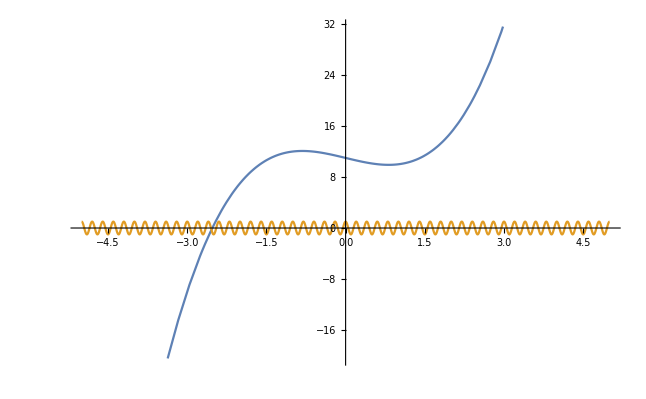

```mathematica
Plot[{f1[x],f3[x]},{x,-5,5}]
```

También es posible graficar superficies en Mathematica, para ello definimos primero la función e incluimos la región del plano en donde queremos graficar la superficie.

```mathematica
f2[x1_,x2_]:=x1^2-x2^2; (* Un paraboloide hiperbólico o la famosa silla de montar *)
```

```mathematica
Plot3D[f2[x1,x2],{x1,-6,6},{x2,-6,6}]
```

-Graphics3D-

Los gráficos se pueden rotar y ampliar, así como exportar en un formato dado: png, pdf, svg, etc (dando clic derecho sobre la imagen)

## Manejo de entidades químicas:

Mathematica trae incorporado un banco de moléculas (limitado en alcance) pero con las moléculas más empleadas en el curso de Química general
Para acceder a las diferentes moléculas usamos la siguiente sintaxis:

```mathematica
Bz = Entity["Chemical","Benzene"]
```

benzene

Se debe introducir el nombre de la molécula en inglés, además se puede consultar una gran cantidad de información sobre la molécula en cuestión:

```mathematica
Bz["BoilingPoint"]
```

80. °C

```mathematica
Bz["MoleculePlot"]
```

-Graphics3D-